#### Approximation of rational polynomials.12

```mathematica
net = NetInitialize @ NetChain[{LinearLayer[30], ElementwiseLayer[Log[1 + (# - 1)]&], LinearLayer[20], Exp, LinearLayer[10], ElementwiseLayer[#&],  LinearLayer[1]}, "Input" -> "Real", "Output" -> NetDecoder["Scalar"]]
```

NetChain[]

```mathematica
dataset = (# -> 1 +  2# + 3#^2 + 4#^4 + 5#^5) &@ RandomReal[{0, 5}, 10000];
```

```mathematica
validationset = (# -> 1 + 1 +  2# + 3#^2 + 4#^4+ 5#^5) &@ RandomReal[{0, 5}, 200];
```

```mathematica
Clear[trainednet]
```

```mathematica
trainednet = NetTrain[net, dataset, ValidationSet->validationset, MaxTrainingRounds->500]
```

NetTrain::arrdiv: Training was aborted because one or more trainable parameters of the net diverged. To avoid this, ensure that the training data has been normalized to have zero mean and unit variance. You can also try specifying a lower "InitialLearningRate" to Method; the value used for this training session was 0.001. Alternatively, you can use the "GradientClipping" option to Method to bound the magnitude of gradients during training.

$Failed

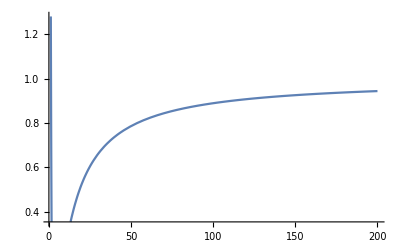

```mathematica
Plot[{Abs[(trainednet[x] - (1 +  2x + 3 x^2 + 4 x^4 + 5 x^5))]/(1 +  2x + 3 x^2 + 4 x^4 + 5 x^5)}, {x, 1, 200}]
```

```mathematica
PDF[NormalDistribution[0,1],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
RandomInteger[{1,3}]
```

1

```mathematica
Keys[dataset1][[ RandomInteger[{1, 4}]]]
```

-4.93122

```mathematica
net1 = NetInitialize @ NetChain[{ LinearLayer[20], ElementwiseLayer[1/E^((# - Keys[dataset1][[RandomInteger[{1, Length[Keys[dataset1]]}]]])^2/2)&], LinearLayer[10], ElementwiseLayer[1/E^((# - Keys[dataset1][[RandomInteger[{1, Length[Keys[dataset1]]}]]])^2/2)&],  LinearLayer[1]}, "Input" -> "Real", "Output" -> NetDecoder["Scalar"]]
```

NetChain[]

```mathematica
dataset1 = (# -> BesselJ[1, #]) &@ RandomReal[{-5, 5}, 100000];
```

```mathematica
validationset1 = (# -> BesselJ[1, #]) &@ RandomReal[{-5, 5}, 200];
```

```mathematica
trainednet1 = NetTrain[net1, dataset1, ValidationSet->validationset1, MaxTrainingRounds->500]
```

NetChain[]

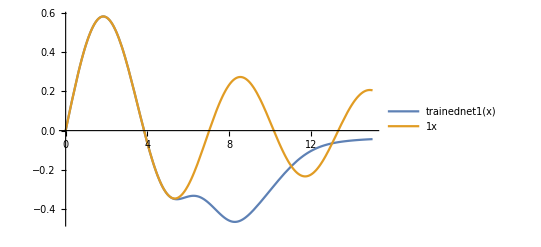

```mathematica
Plot[{trainednet1[x], BesselJ[1, x]}, {x, 0, 15}, PlotLegends-> "Expressions"]
```

```mathematica
Keys[dataset]
```

{3.68087,2.06114,1.28967,2.74497,1.20615,0.361573,3.09642,1.75004,2.18585,0.887561,3.42202,1.38941,4.7456,4.84296,9972,4.29081,1.30678,1.42052,0.177403,1.865,4.85482,3.37289,2.17407,4.47684,3.50745,4.23622,3.31784,1.60467,2.58328}
 |  |  |  |

```mathematica
Length[Keys[dataset]]
```

10000

```mathematica
ccdata = ClusterClassify[Keys[dataset1],100];
```

```mathematica
mean = Mean[dataset1]
```

Mean[{-3.07962,-3.52268,-2.24594,2.53756,1.65775,2.05958,-1.37625,0.39105,3.38252,-4.00163,-0.410515,-0.208776,4.94086,99974,-2.37066,0.664968,-4.95534,3.83068,1.87531,1.35648,0.946725,-0.109541,-2.71,-4.40967,2.28007,3.81873,2.37605}→{1}]
 |  |  |  |

```mathematica
besselApprox = trainednet1[#] &@ Range[-8, 8, 0.01];
bessel = BesselJ[1, #] &@ Range[-8, 8, 0.01];
```

```mathematica
besselRMSE = Sqrt[Mean[(besselApprox - bessel)^2]]
```

0.0506606

0.00701829